## 测地线方程

计算测地线方程。

```mathematica
ChristoffelSymbol1[g_,xx_]:=Inverse[g].(#+Transpose[#,{3,1,2}]-Transpose[#,{2,3,1}])/2&@Grad[g,xx];
```

```mathematica
RiemannTensor[chris_,xx_]:=
Module[{Rie1,Rie3},
Rie1=Outer[D,chris,xx];
Rie3=chris.chris;Simplify[Rie1-Transpose[Rie1,{1,2,4,3}]+Rie3-Transpose[Rie3,{1,4,3,2}]]];
```

```mathematica
ChristoffelSymbol1[DiagonalMatrix[{gt[rr[τ]],gr[rr[τ]],gθ[rr[τ]]}],{tt[τ],rr[τ],θθ[τ]}]
```

{{{0,gt'[rr[τ]]/(2 gt[rr[τ]]),0},{gt'[rr[τ]]/(2 gt[rr[τ]]),0,0},{0,0,0}},{{-(gt'[rr[τ]]/(2 gr[rr[τ]])),0,0},{0,gr'[rr[τ]]/(2 gr[rr[τ]]),0},{0,0,-(gθ'[rr[τ]]/(2 gr[rr[τ]]))}},{{0,0,0},{0,0,gθ'[rr[τ]]/(2 gθ[rr[τ]])},{0,gθ'[rr[τ]]/(2 gθ[rr[τ]]),0}}}

#### Schwarzschild BH

```mathematica
Rs=1;
gtt[r_]:=-(1-Rs/r)
grr[r_]:=1/(1-Rs/r)
gθθ[r_]:=r^2

g=DiagonalMatrix[{gtt[rr[τ]],grr[rr[τ]],gθθ[rr[τ]]}];
geodesics=-ChristoffelSymbol1[g,{tt[τ],rr[τ],θθ[τ]}].{tt'[τ],rr'[τ],θθ'[τ]}.{tt'[τ],rr'[τ],θθ'[τ]}//FullSimplify
```

{(rr'[τ] tt'[τ])/(rr[τ]-rr[τ]^2),(rr[τ]^2 rr'[τ]^2-(-1+rr[τ])^2 tt'[τ]^2)/(2 (-1+rr[τ]) rr[τ]^3)+(-1+rr[τ]) θθ'[τ]^2,-(2 rr'[τ] θθ'[τ])/rr[τ]}

```mathematica
orbitω[r_]:=Sqrt[1/(2r^3)]
```

```mathematica
Flux[r_]:=With[{M=Rs/2},3M^(3/2)/(8Pi r^(5/2)(r-3M))(Sqrt[r/M]-Sqrt[3]/2Log[(Sqrt[r]-Sqrt[3M])/(Sqrt[r]+Sqrt[3M])]-Sqrt[6]+Sqrt[3]/2Log[(Sqrt[2]-1)/(Sqrt[2]+1)])];
```

#### JMN - 1 Metric

Rs=M0 Rb, 0<M0<0.8
when M0>2/3, identical to Schwarzschild BH (has photon sphere).
so we mainly consider the situation where Rb>1.5 Rs

```mathematica
{-(1-M0)(r/Rb)^(M0/(1-M0)),1/(1-M0),r^2}/.M0->Rs/Rb//FullSimplify
```

{-((-1+Rb) (r/Rb)^(1/(-1+Rb)))/Rb,Rb/(-1+Rb),r^2}

Listable Min and Max

```mathematica
myMin[a_,b_]:=a+UnitStep[a-b](b-a)
myMax[a_,b_]:=a+UnitStep[b-a](b-a)
```

```mathematica
Rs=1;
Rb=1.6;
gtt[r_]:=-(1-Rs/myMax[r,Rb]) (myMin[r,Rb]/Rb)^(1/(Rb-1))
grr[r_]:=1/(1-Rs/myMax[r,Rb])
gθθ[r_]:=r^2

g=DiagonalMatrix[{gtt[rr[τ]],grr[rr[τ]],gθθ[rr[τ]]}];
geodesics=FullSimplify[FullSimplify[-ChristoffelSymbol1[g,{tt[τ],rr[τ],θθ[τ]}].{tt'[τ],rr'[τ],θθ'[τ]}.{tt'[τ],rr'[τ],θθ'[τ]}]/.(rr[τ]>Rb):>(rr[τ]≥Rb)]
```

{Piecewise[{{-(1. rr'[τ] tt'[τ])/((-1.+rr[τ]) rr[τ]), rr[τ]≥1.6}, {-(1.66667 rr'[τ] tt'[τ])/rr[τ]^1., True}}],Piecewise[{{-0.0535404 rr[τ]^0.666667 tt'[τ]^2+0.375 rr[τ] θθ'[τ]^2, rr[τ]<1.6}, {(0.5 rr[τ]^2 rr'[τ]^2-0.5 (1.-1. rr[τ])^2 tt'[τ]^2+1. (1.-1. rr[τ])^2 rr[τ]^3 θθ'[τ]^2)/(rr[τ]^3 (-1.+1. rr[τ])), True}}],-(2. rr'[τ] θθ'[τ])/rr[τ]}

```mathematica
orbitω[r_]:=Sqrt[(myMin[r,Rb]/Rb)^(1/(-1+Rb)) /(2 myMax[r,Rb] r^2) ]
```

```mathematica
ClearAll[Fluxsch,Flux];
Fluxsch[r_]:=With[{M=Rs/2},3M^(3/2)/(8Pi r^(5/2)(r-3M))(Sqrt[r/M]-Sqrt[3]/2Log[(Sqrt[r]-Sqrt[3M])/(Sqrt[r]+Sqrt[3M])]-Sqrt[6]+Sqrt[3]/2Log[(Sqrt[2]-1)/(Sqrt[2]+1)])];

Flux[r_]:=With[{M=Rs/2,M0=1/Rb},
If[M0≤1/3,
If[r<Rb,
M0/(4Pi Rb^2)(r/Rb)^((3M0-4)/(2(1-M0))),M0/(4Pi Rb^2)+Fluxsch[r]-Fluxsch[Rb]]
,
If[r<Rb,
M0/(4Pi Rb^2)(r/Rb)^((3M0-4)/(2(1-M0))),
Fluxsch[r]
]]]
```

#### JNW Metric

Listable Min and Max

```mathematica
gg=0.45;

gtt[r_]:=-(1-1/(gg r))^gg
grr[r_]:=1/(1-1/(gg r))^gg
gθθ[r_]:=r^2(1-1/(gg r))^(1-gg)

g=DiagonalMatrix[{gtt[rr[τ]],grr[rr[τ]],gθθ[rr[τ]]}];
geodesics=FullSimplify[FullSimplify[-ChristoffelSymbol1[g,{tt[τ],rr[τ],θθ[τ]}].{tt'[τ],rr'[τ],θθ'[τ]}.{tt'[τ],rr'[τ],θθ'[τ]}]]
```

{-(1. rr'[τ] tt'[τ])/((1-2.22222/rr[τ])^1. rr[τ]^2),((0.5 rr'[τ]^2)/(1-2.22222/rr[τ])^1.-(0.5 tt'[τ]^2)/(1-2.22222/rr[τ])^0.1)/rr[τ]^2+0.611111 θθ'[τ]^2+1. (1-2.22222/rr[τ])^1. rr[τ] θθ'[τ]^2,((-1.22222/(1-2.22222/rr[τ])^1.-2. rr[τ]) rr'[τ] θθ'[τ])/rr[τ]^2}

## 构造 {r,θ}→{θ_0,θ_1,Δt} 关系（2D 光追）

预先设定接受者距离中心的距离R0，一个比较合适的观察者位置是15Rs处，即5倍的最内层稳定圆周轨道（ISCO）处。

{r,θ} 是发射点坐标
θ_0 是接收者接到光的方向与r方向的夹角——ReceiveAngleFunction
θ_1 是被接受者接收到的这一束光，在发出时与r方向夹角——EmitAngleFunction
Δt 是从发出到接收经过的坐标时——DelayFunction

这里只考虑光线绕了小于1.5圈的情况（可以大于半圈）
之所以不考虑转了1.5圈以上的是因为计算表明，转1.5圈以上的时候，其强度至少30倍的弱于转小于一圈的（别的因子影响不大，但是强度Part I一节中计算的因子部分对转角比较敏感），那其实就是看不见了咯……但是如果转1.2圈或者什么，也就是比转0.x圈弱了两三倍，还是非常值得考虑的。

```mathematica
$HistoryLength=0;
```

```mathematica
R0=15Rs;
Rmax=15Rs+1.*^-5;
```

θ0是接收角
Schwarzschild

```mathematica
parfuncraw=ParametricNDSolveValue[{{tt''[τ],rr''[τ],θθ''[τ]}==geodesics,{tt'[0],rr'[0],θθ'[0]}=={Sqrt[-grr[R0]/gtt[R0]],-Cos[θ0],Sqrt[grr[R0]/gθθ[R0]]Sin[θ0]},{tt[0],rr[0],θθ[0]}=={0,R0,0},
WhenEvent[1.01Rs≥rr[τ],{state=1,"StopIntegration"}],
WhenEvent[rr[τ]≥Rmax,{state=2,"StopIntegration"}],
WhenEvent[θθ[τ]≥θmax,{state=3,"StopIntegration"}]},{tt[τ],rr[τ],θθ[τ]},{τ,0,1000},{θ0,θmax},Method->{"ParametricCaching"->None}];
parfunc[θ_,θmax_:3.1Pi]:=parfuncraw[θ,θmax];
```

JMN-1 (和前面唯一的差别就是终止条件，WhenEvent有差）

```mathematica
parfuncraw=ParametricNDSolveValue[{{tt''[τ],rr''[τ],θθ''[τ]}==geodesics,{tt'[0],rr'[0],θθ'[0]}=={Sqrt[-grr[R0]/gtt[R0]],-Cos[θ0],Sqrt[grr[R0]/gθθ[R0]]Sin[θ0]},{tt[0],rr[0],θθ[0]}=={0,R0,0},
WhenEvent[rr[τ]≥Rmax,{state=2,"StopIntegration"}],
WhenEvent[θθ[τ]≥θmax||θθ[τ]<-0.5Pi,{state=3,"StopIntegration"}]},{tt[τ],rr[τ],θθ[τ]},{τ,0,10000},{θ0,θmax},Method->{"ParametricCaching"->None},MaxSteps->Infinity,MaxStepSize->0.02];
parfunc[θ_,θmax_:3.1Pi]:=parfuncraw[θ,θmax];
```

对不同的θ0，反向追光，记录光线轨迹上的{θ_0,θ_1,Δt}。
为了精度和方便考虑，我们这里认为所有物体都在2.5~12.5 Rs之内（观察者认为在15 Rs处，ISCO于3Rs处)。

```mathematica
ϕmax=540Degree;
```

```mathematica
datp=DeleteDuplicatesBy[Flatten[Reap[
Block[{θrange={-0.1,1.45},tab,pf,state},
Table[
tab=Table[
pf=parfuncraw[θ,θmax];
With[{τmax=pf[[1,0,1,1,2]],df=D[Rest@pf,τ],f=Rest@pf},Block[{τ=Range[RandomReal[{0,τmax/500}],τmax,τmax/500]},Sow@Select[Thread[(Thread@f->Thread@{θ,ArcTan[-df[[1]],df[[2]] Sqrt[gθθ[f[[1]]]/grr[f[[1]]]]],pf[[1]]})],2.4Rs<#[[1,1]]<12.5Rs&&(θmax-0.7Pi<#[[1,2]]<θmax-0.01Pi)&]]];
{θ,state}
,{θ,Subdivide[θrange[[1]],θrange[[2]],100]}];
θrange={tab[[FirstPosition[tab,{_,3}][[1]]-1,1]],tab[[FirstPosition[tab,{_,2}][[1]],1]]};
,{θmax,0.5Pi,4Pi,0.5Pi}]]][[2]]
,2],First];
```

对于JMN-1 Metric, 可能没有photon sphere，在这种情况下代码需要略微调整一下。

对于Rb=1.6

```mathematica
ϕmax=540Degree;
```

对于Rb=2.0

```mathematica
ϕmax=505Degree;
```

对于Rb=3.3

```mathematica
ϕmax=275Degree;
```

```mathematica
datp=DeleteDuplicatesBy[Flatten[Reap[
Block[{θrange={-0.1,1.45},tab,pf,state},
Table[
state=1;
tab=Table[
pf=parfuncraw[θ,θmax];
With[{τmax=pf[[1,0,1,1,2]],df=D[Rest@pf,τ],f=Rest@pf},Block[{τ=pf[[1,0,3,1,;;;;5]]},Sow@Select[Thread[(Thread@f->Thread@{θ,ArcTan[-df[[1]],df[[2]] Sqrt[gθθ[f[[1]]]/grr[f[[1]]]]],pf[[1]]})],#[[1,1]]<12.5Rs&&(#[[1,2]]<Min[θmax-0.01Pi,ϕmax+1Degree])&]]];
{θ,state}
,{θ,Rest@Subdivide[θrange[[1]],θrange[[2]],150]}];
θrange={0,tab[[FirstPosition[tab,{_,2}][[1]],1]]};
,{θmax,0.5Pi,4Pi,0.5Pi}]]][[2]]
,2],First];
```

ParametricNDSolveValue::ndsz: At τ == 14.273, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At τ == 14.2738, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At τ == 14.2752, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

ParametricNDSolveValue::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between τ = 32.6553 and τ = 32.6753.

ParametricNDSolveValue::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between τ = 33.2995 and τ = 33.3195.

绘制采样点（太密了没必要，太疏了结果不精确），这里限制精度的主要是下一部分中的反向追踪那块。

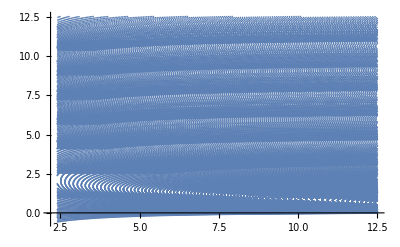

```mathematica
datp[[;;,1]]+=RandomReal[1.*^-5,Dimensions@datp[[;;,1]]];
ListPlot[datp[[;;,1]],PlotRange->Full]
```

插值函数

```mathematica
ReceiveAngleFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,1]]}],InterpolationOrder->1];
EmitAngleFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,2]]}],InterpolationOrder->1];DelayFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,3]]}],InterpolationOrder->1];
```

测试、画图

```mathematica
Through[{ReceiveAngleFunction,EmitAngleFunction,DelayFunction}[4,ϕmax-10Degree]]
```

{0.168229,2.54376,40.5397}

```mathematica
Plot3D[#[x,y],{x,0,12},{y,0,ϕmax},PlotRange->Full]&/@{ReceiveAngleFunction,EmitAngleFunction,DelayFunction}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 强度 Part 1

这一步我们只考虑由于“距离”远近带来的强度衰减。
强度与距离远近的关系在正常平直的时空中是二次方反比，这是因为假如我们摆个圆盘，那圆盘距离发光点越远，圆盘相对发光点的张角就越小，这个关系是二次方。这里光线是弯曲的，所以关系可能很复杂，我们只能数值求解。

我们需要计算两个方向上的光发散。垂直平面和平面内。垂直平面可以直接通过前面得到的θ_0,θ_1计算，而平面内则要反向追踪光线获得。原理如附图。

Schwarzschild & JMN-1

```mathematica
parfuncrev=ParametricNDSolveValue[Evaluate@{{tt''[τ],rr''[τ],θθ''[τ]}==geodesics,{tt'[0],rr'[0],θθ'[0]}=={FullSimplify[Sqrt[-grr[R1]/gtt[R1]],Assumptions->(R1>1)],Cos[θ0],-FullSimplify[Sqrt[grr[R1]/gθθ[R1]],Assumptions->(R1>1)]Sin[θ0]},{tt[0],rr[0],θθ[0]}=={0,R1,θ1},WhenEvent[rr[τ]==R0,"StopIntegration"]},{tt[τ],rr[τ],θθ[τ]},{τ,0,100},{θ0,R1,θ1}];
```

验证反向光追的精度，蓝线为正向光追，绿线为反向光追。

18.7478

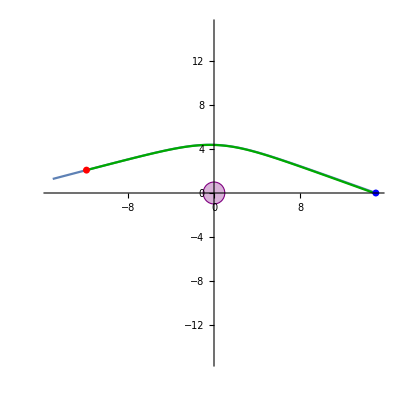

```mathematica
{pr,pt}={12,170Degree};
ReceiveAngleFunction[pr,pt]/Degree
pf=parfuncraw[ReceiveAngleFunction[pr,pt],5Pi];
τmax=pf[[1,0,1,1,2]];

fig1=ParametricPlot[Evaluate[#2{Cos[#3],Sin[#3]}&@@pf],{τ,0,τmax},Epilog->{Purple,Opacity@.3,EdgeForm@Directive[Purple,Opacity@1],Disk[],Red,AbsolutePointSize@5,Opacity@1,Point[pr{Cos[pt],Sin[pt]}],Blue,Point[{R0,0}]},PlotRange->{{-1,1},{-1,1}}1.01Rmax];

pf=parfuncrev[EmitAngleFunction[pr,pt]+0.001,pr,pt];
τmax=pf[[1,0,1,1,2]];
fig2=ParametricPlot[Evaluate[#2{Cos[#3],Sin[#3]}&@@pf],{τ,0,τmax},PlotRange->{{-1,1},{-1,1}}Rmax,PlotStyle->Darker@Green];

Show[fig1,fig2]
```

```mathematica
pf[[1,0,1,1,2]]
```

23.0924

打点，逐个点计算光强度因子。

```mathematica
Δϕ=1.*^-5;
```

```mathematica
Dynamic[{R,θ}]
```

Schwarzschild max @ 540 degree, R starting from 2.9 Rs
JMN-1 max @ 480 degree, R starting from -0.1 Rs

```mathematica
intensity=Catenate@Table[{{R,θ}, With[{θ=Abs[θ],R=Abs[R]},Abs[Sin[EmitAngleFunction[R,θ]]/Sin[θ]]*(Δϕ/(Cos[ReceiveAngleFunction[R,θ]]* Subtract@@(With[{f=parfuncrev[EmitAngleFunction[R,θ]+# Δϕ,R,θ]},f[[3,0]]@f[[1,0,1,1,2]]]&/@{-1,1})))]},{R,2.9Rs,12.1Rs,0.2Rs},{θ,-0.5Degree,ϕmax,1Degree}];
```

```mathematica
IntensityFunction1=Interpolation[intensity];
```

相对亮度分布，假如离源较近的话基本和平直空间一致，呈平方反比律。背面光强极强至发散（引力透镜），绕一圈的话强度就很低了。

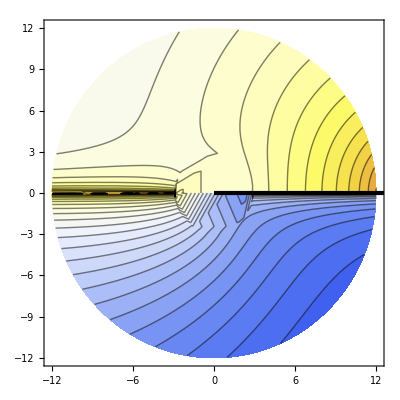

```mathematica
Show[ListContourPlot[Join[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,0<#[[1,2]]<1.2Pi&],Append[#[[1]]{Cos[#[[2]]],-Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,0<#[[1,2]]<.5Pi&]],RegionFunction->Function[{x,y},y>0&&x^2+y^2<(12Rs)^2],PlotRange->{-10,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-10,6,.5],InterpolationOrder->3],
ListContourPlot[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,.8Pi<#[[1,2]]&],RegionFunction->Function[{x,y},y<0&&x^2+y^2<(12Rs)^2],PlotRange->{-10,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-10,6,.5],InterpolationOrder->3],Epilog->{AbsoluteThickness@3,Black,Line[{{0,0},{15,0}}]}]
```

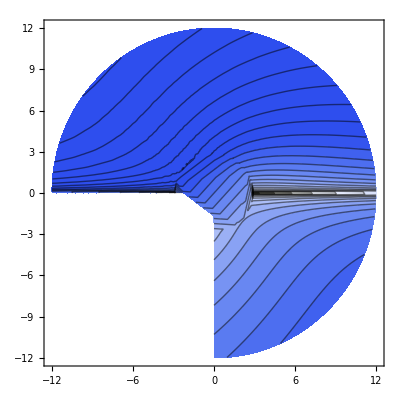

```mathematica
ListContourPlot[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,1.45Pi<#[[1,2]]<ϕmax&],RegionFunction->Function[{x,y},-.5Pi<ArcTan[x,y]<ϕmax-2Pi&&x^2+y^2<(12Rs)^2],PlotRange->{-20,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-20,6,.5],AspectRatio->Automatic,InterpolationOrder->3]
```

平方反比律验证，在观测者和源比较接近的时候（这里取距离小于3 Rs）和平方反比预测一致。
横轴：平方反比律的预测，纵轴：实际结果

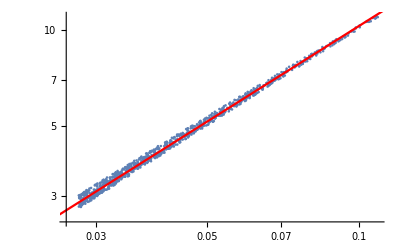

```mathematica
samplereg=ImplicitRegion[x^2+y^2≤(12Rs)^2&&(15Rs-x)^2+y^2≤(6Rs)^2&&y>0,{x,y}];
samples={1/((15Rs-#1)^2+#2^2),IntensityFunction1[Norm[{#1,#2}],ArcTan[#1,#2]]}&@@@RandomPoint[samplereg,1000];
fit=FindFit[samples,k x,k,x];
Show[ListLogLogPlot[samples],Plot[Log[k]+x/.fit,{x,-10,3},PlotStyle->Red]]
```

## 频移

输入{R1,θ,ϕ},{vr,vθ,vϕ},T,I，我们希望得到新角度&新光谱&新光谱强度。

很显然，观测到的角度为{θ_obs,ϕ_obs}={ReceiveAngleFunction[R1,θ],ϕ}
但是颜色、强度和被观测到的时间还有待商榷

先看颜色，两部分，发出时频移（狭相）和传播时频移（广相）

发出时ω_0=ω·v，接收到ω_1=ω√(g_00'/g_00)，其中ω是刚发射出来时从地系看到的频率。

先写两个很好用的辅助函数，第一个计算固定dr/dt,dθ/dt,dϕ/dt（注意，是dt）的时候其绝对速度β
另一个则是计算光线方向与速度方向夹角的：

```mathematica
Calcβ[{R1_,θ_,ϕ_},{vr_,vθ_,vϕ_}]:=Evaluate@Sqrt[-(vr^2 grr[R1]+gθθ[R1](vθ^2+(Sin[θ]vϕ)^2))/gtt[R1]]
```

```mathematica
Calcβ[{{2,3},{.3,.4},{.3,.2}},{{.1,.2},{.3,.2},{.1,.1}}]
```

{0.875778,0.806519}

Input should be a list.

```mathematica
CalcCosAngle[{R1_,θ_,ϕ_},{vr_,vθ_,vϕ_}]:=With[{v={vr Sqrt[grr[R1]/gθθ[R1]],vθ,Sin[θ]vϕ}},MapThread[With[{θ0=EmitAngleFunction[R1,#1]},
With[{vnormed=MapThread[Normalize@*List,v]},MapThread[Dot,{vnormed,Thread@{Cos[θ0],#2 Sin[θ0],0}},1]]]&,{{θ,2Pi-θ,2Pi+θ},{-1,1,-1}}]]
```

```mathematica
CalcCosAngle[{4,{30Degree,20Degree},0},{{.2,.03},{.1,.2},{.3,.1}}]
```

{{-0.047735,-0.350611},{-0.018188,0.406821},{-0.462343,-0.390191}}

```mathematica
FrequencyMult[R1_,β_,cos_]:=Sqrt[gtt[R1]/gtt[R0]]*Sqrt[1-β^2]/(1-β cos)
```

```mathematica
FrequencyIntensityMult[R1_,β_,cos_]:=(gtt[R1]/gtt[R0])*(1-β^2)/(1-β cos)
```

## 强度 Part 2

在我们计算最终被观测到的强度时有两个部分：
1. 发出者发出的时候强度分布（和速度及发射角有关）
这其实是在讨论光发出的立体角将如何重新分布，如果发射体本征系中θ变成了地系下的θ’，那么θ方向角度变为dθ’/dθ倍，而ϕ方向变为sin(θ’)/sin(θ)倍，故在单位立体角内由该效应会加强dθ/dθ’*sin(θ)/sin(θ’)倍。

2. 由于频移/光子密度改变带来的强度改变，由于频率改变和光子密度改变其实是一个事情，所以两个合起来恰好是FrequencyMult^2
3. 广义相对论带来的透镜效应（也就是前面强度 Part 1中讨论的）

为了避免重复计算，实际光强是FrequencyMult^2 * IntensityFunction1 * IntensityMult2，相当于IntensityMult1只包括了效应1。其中第一项对应 (dθ/dθ’), 第二项对应 sin (θ)/sin(θ’)。因为面积是sin(θ) dθ dϕ

```mathematica
With[{θstatic=ArcCos[(Cos[t]-β)/(1-Cos[t]β)]},
FullSimplify[D[θstatic,t]*Sin[θstatic]/Sin[t]]]
```

-(-1+β^2)/(-1+β Cos[t])^2

```mathematica
IntensityMult2[β_,cos_]:=(Sqrt[1-β^2]/(1-β cos))^2
```

## Time - Observed Position

要做一个真实的模拟，不应该忽略掉光传播的时间！我们要在少量的粒子里面体现一下时间的变化。
首先给出轨迹：设赤道面偏角为θ1，转角为ϕ1，我们可以推得极坐标夹角:
{θ,ϕ}={ArcCos[Sin[ϕ1]Sin[θ1]],ArcTan[Cos[ϕ1],Sin[ϕ1]Cos[θ1]]}

这里ϕ的运行速率和轨道半径R1的关系为：ω_ϕ=Sqrt[R_s c^2/(2R^3)],假如我们取时间单位Rs/c，距离单位Rs，那么有T=T0+Sqrt[2 R^3]ϕ

后面我们假定θ1=70Degree, 在计算时R1暂时取4Rs。发现其实这个time delay还是很短的（毕竟即使是在ISCO上速度也就是1/3光速而已），如下图所示。其中横轴为ϕ1，即轨道角度，纵轴T为接受到的时间。直线是固定delay的参考。

所以，对于一个固定轨道上运行的粒子（即给定R1，θ1和初始ϕ1），我们可以轻易地给出其被观察的角度t(ϕ1)关系，这是一个一一对应的函数，那么我们也就可以取逆得到ϕ1(t)，就可以根据ϕ1计算别的效应，并画图了~

函数将返回三个数值，分别对应光走了+θ,2π-θ,2π+θ的三种情况。

```mathematica
GenerateAngleFunctions[R1_,θ1_]:=Block[{ϕ1},
With[{interpol=Interpolation@Table[{DelayFunction[R1,#]+Sqrt[2 R1^3]ϕ1,ϕ1},{ϕ1,0.,2Pi,10.Degree}]},
With[{ts=interpol[[1,1,1]],tperiod=2.Pi Sqrt[2 R1^3]},Function[t,interpol[t-Floor[t-ts,tperiod]]]]]&/@({#,2Pi-#,2Pi+#}&@ArcCos[Sin[ϕ1]Sin[θ1]])]
```

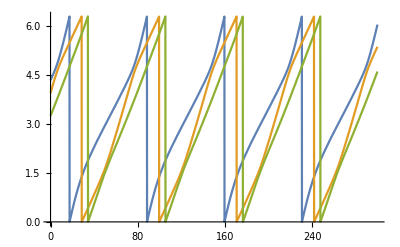

```mathematica
Plot[Evaluate@Through[GenerateAngleFunctions[4Rs,70Degree][t]],{t,0,300}]
```

## All in All Rendering --- Single Point

一个返回函数 f[t]的函数。
这个f[t]的输入是观测时间，而输出则是一个完整的Graphics图元，表示了被观测到的位置（观测点为{0,0,0}）及颜色（包括强度）

这里考虑的是一个沿着圆轨道运行的粒子，认为它是一个黑体。
R1是轨道半径, θ1,t1,γ1是三个欧拉角, θ1定义如前, t1对应ϕ1/ω,代表了时间上的offset, γ1 则代表了轨道面相对于极轴的旋转.
T0代表了原始的温度（在其他情况下可以改成任何控制颜色的参数）
I0代表了物体原本的发射强度

选项ColorFunction->cf是渲染颜色时用到的颜色函数，默认为PhysicalColor包内的TemperatureColor函数
选项ColorFunctionScaling->colorfunc是渲染颜色时用的rescale方法，默认不scale
选项IntensityFunctionScaling->intfunc是渲染强度时用的rescale方法，默认不scale

要求后面两个Rescale函数都可以作用于List。

对于一个单色光来说，颜色和强度的换算是很简单的，就是频率乘个频率因子，强度乘个强度因子就可以了，这都是前面讨论的内容。

但是这里很重要的一点是，黑体辐射是一个连续谱，其频移时在可见光波段强度分布（也就是颜色）的变化如下：
若原来颜色是color(T)，则在ν->k ν的变换下，颜色变为color(k T)
若原来强度是I(T)，则变为f(k)/k^4 I(kT)，其中f(k)为单频光强度变化因子，即前面讨论的内容。

关于这个的讨论不是很Trivial，我们来解释一下。首先看普朗克的黑体辐射定律，单位频率内能量密度为：
E(ν,T)=const*ν^3/(exp(hν/kT)-1)
由此可得：
E(λν,T)=λ^3 E(ν,T/λ)

我们来看下视明度是怎么定义的：
I(T)=∫_νmin^νmax E(ν,T)S(ν)ⅆν
其中S(ν)是视明度函数，代表了单位能量的，频率为ν的光，视明度是多少。

那在频移ν->k ν之后，我们假设能量密度函数变为了E’(ν,T)，这时明度为：
I’(T)=∫_νmin^νmax E’(ν,T)S(ν)ⅆν

考虑频率ν~ν+dν内的光，之前这段光强度为：
E(ν,T)dν，而现在其频率变为了kν~kν+kdν，强度增强为f(k)倍，即有：
f(k)E(ν,T)dν=E’(kν,T)kdν
借助这个关系我们可以化简前面的I’(T)了：
I’(T)=∫_νmin^νmax E’(ν,T)S(ν)ⅆν
         =f(k)/k∫_νmin^νmax E(ν/k,T)S(ν)ⅆν
         =f(k)/k^4∫_νmin^νmax E(ν,k T)S(ν)ⅆν
         =f(k)/k^4 I(k T)
         
完美！而且同样遵循这个过程，只不过把S(ν)换成色感的函数，我们也知道了颜色其实只是变为k T时对应的颜色而已。

```mathematica
<<PhysicalColor`
```

```mathematica
IntensityFunctionScaling::usage="Scale Intensity.";
Protect@IntensityFunctionScaling;
```

```mathematica
Options[RenderFunc]={ColorFunction->TemperatureColor,ColorFunctionScaling->(#&),IntensityFunctionScaling->(#&),"StaticObserver"->True};
```

```mathematica
RenderFunc[R1_,{θ1_,t1_,γ1_},{T0_,I0_},OptionsPattern[]]:=
Function[t,Through[#[t]]]&@Module[{
(*Velocity of observer*)
vobs=N@Sqrt[(1-Rs/R0)Rs/(2R0)],
(*list of ϕ1 parameters*)
ϕ1l=Range[0.,2Pi,1Degree],
(*Polar coordinates θ and ϕ*)
θl0,ϕl0,
(*velocity of object and its norm*)
vrl,vθl,vϕl,vnorml
},
(*Polar coordinate θ*)
θl0=ArcCos[Sin[ϕ1l]Sin[θ1]];

(*Original ϕ*)
ϕl0=ArcTan[Cos[ϕ1l],Sin[ϕ1l]Cos[θ1]]+γ1;

(*velocity of object*)
vrl=ConstantArray[0,Length@ϕ1l];
vθl=-(Cos[ϕ1l]Sin[θ1])/Sqrt[1 - Sin[θ1]^2Sin[ϕ1l]^2]*Sqrt[Rs/(2R1^3)];
vϕl=1/(Cos[ϕ1l]^2/Cos[θ1]+Cos[θ1]Sin[ϕ1l]^2)*Sqrt[Rs/(2R1^3)];

(*velocity norm*)
vnorml=Calcβ[{R1,θl0,0},{vrl,vθl,vϕl}];

MapThread[Module[{
(*Observed ϕ1 parameter - t*)
ϕ1t=#3,
(*actual θ of object*)
θl=#1,
(*angle between velocy and ray*)
cosl=#4,
(*Observed values - ϕ1*)
(*Geometry*)
θobsl,ϕobsl=ϕl0+#2,
(*Frequency and intensity shift*)
freqobsl,intobsl,
(*helper function*)
helpf
},
θobsl=ReceiveAngleFunction[R1,θl];

(*Frequency*)
freqobsl=FrequencyMult[R1,vnorml,cosl];

(*Process with the non-static observer*)
If[OptionValue["StaticObserver"]=!=True,
Module[{θtransl,ϕtransl,δ=ArcSin[vobs]},
(*Geometrics, static frame*)
θtransl=ArcCos[Sin[θobsl]Cos[ϕobsl]];
ϕtransl=ArcTan[Sin[θobsl]Sin[ϕobsl],Cos[θobsl]];
(*Frequency shift due to movement of observer, intensity shift is calculated together later*)
freqobsl*=(1+vobs Cos[θtransl])/Sqrt[1-vobs^2];
(*Angle shift due to movement of observer*)
θtransl=ArcCos[(vobs+Cos[θtransl])/(1+vobs Cos[θtransl])];
(*Transform back*)
(*Here we change the center of viewing angle so that the black hole's center is at {0,0}*)
θobsl=ArcCos[Sin[δ]Cos[θtransl]+Cos[δ]Sin[θtransl]Sin[ϕtransl]];
ϕobsl=ArcTan[Cos[δ]Cos[θtransl]-Sin[δ]Sin[θtransl]Sin[ϕtransl],Sin[θtransl]Cos[ϕtransl]]
]
];

ϕobsl=Catenate[MapIndexed[#1+2Pi#2[[1]]&,Split[ϕobsl,Less]]];

(*Intensity*)
intobsl=freqobsl^2*IntensityFunction1[R1,θl]*IntensityMult2[vnorml,cosl]*TemperatureIntensity[freqobsl T0]/TemperatureIntensity[T0]/freqobsl^4;

(*Helper function to construct interpolating functions*)
helpf[l_]:=Interpolation[Thread[{ϕ1l,l}]];

With[{
cf=OptionValue[ColorFunction],
(*Interpolating functions*)
t11=t1,
ϕ1f=#3,
θfunc=helpf[θobsl],
ϕfunc=helpf[ϕobsl],
freqfunc=helpf[OptionValue[ColorFunctionScaling][T0 freqobsl]],
intfunc=helpf[OptionValue[IntensityFunctionScaling][I0 intobsl]]
},
 
(*Final function*)
Function[t,
With[{ϕ11=ϕ1f[t+t11]},
{Append[cf[freqfunc[ϕ11]],intfunc[ϕ11]],
With[{θ=θfunc[ϕ11],ϕ=ϕfunc[ϕ11]},
(*Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}]*)Point[Tan[θ]{Cos[ϕ],Sin[ϕ]}]]}
]]
]
]&,{{θl0,2Pi-θl0,2Pi+θl0},{0,Pi,0},GenerateAngleFunctions[R1,θ1],CalcCosAngle[{R1,θl0,0},{vrl,vθl,vϕl}]}]]
```

内置的Rasterize的最大问题是很难处理好低亮度区域，会显著地损失掉颜色的位数。为了实现后期的亮度变换，我们只能勉为其难的生成一组照片（这里两张就够了，比较幸运），其中第二张相比于前一组亮度被提升了16倍，这样就可以分级调节，实现HDR效果。
这段代码中无关部分耗时约2s，其实还是可以忍受的。

```mathematica
HDRRasterize[gr_Graphics,convertfunc_,opts:OptionsPattern[Rasterize]]:=
Module[{rasterl=Join[ColorSeparate[ColorConvert[Rasterize[gr,opts],"HSB"]],ColorSeparate[ColorConvert[Rasterize[gr/.RGBColor[r_,g_,b_,op_]:>RGBColor[r,g,b,16 op],opts],"HSB"]]],mask,invmask},
mask=Binarize[rasterl[[3]],1/16];
invmask=1-mask;
ColorCombine[{
mask*rasterl[[1]]+invmask*rasterl[[4]],
mask*rasterl[[2]]+invmask*rasterl[[5]],
mask*convertfunc[rasterl[[3]]]+invmask*convertfunc[rasterl[[6]]/16.]},"HSB"]
]
```

```mathematica
npts=500;
rflist=MapThread[Function[{R1,θ1,t1,γ1,T0,I0},RenderFunc[R1,{θ1,t1,γ1},{T0,I0},"StaticObserver"->True(*,IntensityFunctionScaling->(.7(#/.5)^0.5&)*)]],
{RandomReal[{3.1,12},npts],
RandomReal[-{83,86}Degree,npts],
RandomReal[{0,10000},npts],
RandomReal[15Degree+{-2,2}Degree,npts],
RandomReal[{4000,10000},npts],
RandomReal[{.03,.1},npts]
}
];
```

```mathematica
npts=500;
rflist=MapThread[Function[{R1,θ1,t1,γ1,T0,I0},RenderFunc[R1,{θ1,t1,γ1},{T0,I0},"StaticObserver"->True(*,IntensityFunctionScaling->(.7(#/.5)^0.5&)*)]],
{Rest@Subdivide[3,9,npts],
ConstantArray[-85Degree,npts],
ConstantArray[0,npts],
ConstantArray[15Degree,npts],
ConstantArray[10000,npts],
ConstantArray[.1,npts]
}
];
```

```mathematica
g=Graphics[{(*AbsolutePointSize@.1,White,Point[{Sin[20Degree]Cos[#],Sin[20Degree]Sin[#],Cos[20Degree]}&/@Range[0.,360.Degree,60.Degree]],*)AbsoluteThickness@2,Map[Line[#[[;;,2,1]],VertexColors->MapThread[Function[{col,mult},MapAt[mult^2*#&,col,4]],{#[[;;,1]],Subdivide[Length[#]-1]}]]&,Reverse@Transpose[Through[rflist[#]]&/@(Range[0,30,.1]),{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}];
```

```mathematica
g=Graphics[{AbsoluteThickness@2,Map[Line[#[[;;,2,1]],VertexColors->#[[;;,1]]]&,Reverse@Transpose[Through[rflist[#]]&/@(Range[0,30,.1]),{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}];
```

无Gamma修正（像素值是亮度）

```mathematica
Rasterize[g,ImageSize->{1920,1080}/5]
```

-Graphics-

Gamma修正（看屏幕看到的亮度是实际亮度）

```mathematica
res=HDRRasterize[g,#^(1/4)&,ImageSize->{1920,1080}/3]
```

-Graphics-

```mathematica
TemperatureColor[20000]
```

RGBColor[0.6784313725490196, 0.7568627450980392, 1.]

```mathematica
TemperatureColor[4000]
```

RGBColor[1., 0.8352941176470589, 0.6313725490196078]

```mathematica
1.1ColorConvert[res,"RGB"]
```

-Graphics-

-Graphics-

```mathematica
Clear@g
```

#### Parallel

```mathematica
tlist=Range[0,20,.05];

CloseKernels[];
LaunchKernels@8;
ParallelEvaluate[<<PhysicalColor`];
SetSharedVariable[count];
SetSharedVariable[tlist]

count=0;
Dynamic[Row[{count,"/",Length@tlist}]]
ProgressIndicator[Dynamic[count/Length@tlist]]
Dynamic[Row[{"Time Left: ",(Now-tstart)*(Length@tlist-count)/count}],TrackedSymbols:>{count}]
```

```mathematica
tstart=Now;
count=0;
With[{nbdir=NotebookDirectory[]},
ParallelDo[
Export[nbdir<>"IMG\\T_"<>IntegerString[num,10,3]<>".png",HDRRasterize[Graphics[{AbsoluteThickness@2,Map[Line[#[[;;,2,1]],VertexColors->MapThread[Function[{col,mult},MapAt[mult^2*#&,col,4]],{#[[;;,1]],Subdivide[Length[#]-1]}]]&,Reverse@Transpose[Through[rflist[#]]&/@(tlist[[num]]+Range[0,3,.1]),{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}],#^(1/2.2)&,ImageSize->{1920,1080},ImageResolution->72]];
count++,{num,Length@tlist}
]]//AbsoluteTiming
```

{15591.5,Null}

#### No redundant calculation Version

```mathematica
Monitor[
i=1;
BlockMap[
Export["C:\\Users\\u8004586\\Desktop\\IMG1\\T_"<>IntegerString[i++,10,3]<>".jpg",Rasterize[Graphics[{(*AbsolutePointSize@.1,White,Point[{Sin[20Degree]Cos[#],Sin[20Degree]Sin[#],Cos[20Degree]}&/@Range[0.,360.Degree,60.Degree]],*)AbsoluteThickness@3,Map[Line[#[[;;,2,1]],VertexColors->MapThread[Darker[#1,#2]&,{#[[;;,1]],1-Subdivide[Length[#]-1]}]]&,Reverse@Transpose[#[[;;;;2]],{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}],ImageSize->{1920,1080}]]&,
Through[rflist[#]]&/@(Range[0,25,.05]),100,1],i]
```

$Aborted

## Waste

```mathematica
Graphics3D[{AbsolutePointSize@2,Reverse@Transpose[Through[rflist[#]]&/@Range[0,5,.05],{2,3,1}]},Axes->False,Boxed->False,Background->Black,ViewPoint->{0,0,-1.5},ViewCenter->{{0,0,1},ImageScaled[{.5,.5}]},ViewVertical->{.3,-1, 0}]
```

```mathematica
Graphics3D[{AbsolutePointSize@1.2,(*White,Point[{Sin[20Degree]Cos[#],Sin[20Degree]Sin[#],Cos[20Degree]}&/@Range[0.,360.Degree,60.Degree]],*)Reverse@Transpose[Through[rflist[#]]&/@Range[0,5,.05],{2,3,1}]},Axes->False,Boxed->False,Background->Black,ImageSize->{500,Automatic}]
```

Obsolete Function

```mathematica
RenderFunc[R1_,{θ1_,t1_,γ1_},{T0_,I0_},OptionsPattern[]]:=
Module[{
(*Observed ϕ1 parameter - t*)
ϕ1t1,ϕ1t2,ϕ1t3,
(*list of ϕ1 parameters*)
ϕ1l=Range[0.,2Pi,1Degree],
(*list of polar coordinates θ and ϕ*)
θl,
(*velocity of object*)
vrl,vθl,vϕl,
(*velocity norm and angle with ray*)
vnorml,cosl1,cosl2,cosl3,
(*Parameters list - ϕ1*)
θfuncl1,ϕfuncl1,freqfuncl1,intfuncl1,
θfuncl2,ϕfuncl2,freqfuncl2,intfuncl2,
θfuncl3,ϕfuncl3,freqfuncl3,intfuncl3,

(*helper function*)
anglesort,
helpf
},

(*observed ϕ1 parameter - t*)
{ϕ1t1,ϕ1t2,ϕ1t3}=GenerateAngleFunctions[R1,θ1];

(*Parameters - observed ϕ1 parameter*)
θl=ArcCos[Sin[ϕ1l]Sin[θ1]];

(*velocity of object*)
vrl=ConstantArray[0,Length@ϕ1l];
vθl=-(Cos[ϕ1l]Sin[θ1])/Sqrt[1 - Sin[θ1]^2Sin[ϕ1l]^2]*Sqrt[Rs/(2R1^3)];
vϕl=1/(Cos[ϕ1l]^2/Cos[θ1]+Cos[θ1]Sin[ϕ1l]^2)*Sqrt[Rs/(2R1^3)];

(*velocity norm and angle with ray*)
vnorml=Calcβ[{R1,θl,0},{vrl,vθl,vϕl}];
{cosl1,cosl2,cosl3}=CalcCosAngle[{R1,θl,0},{vrl,vθl,vϕl}];

(*Parameters - ϕ1*)
(*Geometric*)
θfuncl1=ReceiveAngleFunction[R1,θl];
θfuncl2=ReceiveAngleFunction[R1,2Pi-θl];
θfuncl3=ReceiveAngleFunction[R1,2Pi+θl];

ϕfuncl1=ArcTan[Cos[ϕ1l],Sin[ϕ1l]Cos[θ1]]+γ1;
ϕfuncl2=ϕfuncl1+Pi;
ϕfuncl3=ϕfuncl1;

(*Frequency*)
freqfuncl1=FrequencyMult[R1,vnorml,cosl1];
freqfuncl2=FrequencyMult[R1,vnorml,cosl2];
freqfuncl3=FrequencyMult[R1,vnorml,cosl3];


anglesort[s_]:=Catenate[MapIndexed[#1+2Pi#2[[1]]&,Split[s,Less]]];
(*Process with the non-static observer*)
If[OptionValue["StaticObserver"]=!=True,
Module[{vobs=Sqrt[(1-Rs/R0)Rs/(2R0)],
θobs1,ϕobs1,
θobs2,ϕobs2,
θobs3,ϕobs3},
(*Geometrics, static frame*)
θobs1=ArcCos[Sin[θfuncl1]Cos[ϕfuncl1]];
ϕobs1=ArcTan[Sin[θfuncl1]Sin[ϕfuncl1],Cos[θfuncl1]];
θobs2=ArcCos[Sin[θfuncl2]Cos[ϕfuncl2]];
ϕobs2=ArcTan[Sin[θfuncl2]Sin[ϕfuncl2],Cos[θfuncl2]];
θobs3=ArcCos[Sin[θfuncl3]Cos[ϕfuncl3]];
ϕobs3=ArcTan[Sin[θfuncl3]Sin[ϕfuncl3],Cos[θfuncl3]];
(*Frequency shift due to movement of observer, intensity shift is calculated together later*)
freqfuncl1*=(1+vobs Cos[θobs1])/Sqrt[1-vobs^2];
freqfuncl2*=(1+vobs Cos[θobs2])/Sqrt[1-vobs^2];
freqfuncl3*=(1+vobs Cos[θobs3])/Sqrt[1-vobs^2];
(*Angle shift due to movement of observer*)
θobs1=ArcCos[(vobs+Cos[θobs1])/(1+vobs Cos[θobs1])];
θobs2=ArcCos[(vobs+Cos[θobs2])/(1+vobs Cos[θobs2])];
θobs3=ArcCos[(vobs+Cos[θobs3])/(1+vobs Cos[θobs3])];
(*Transform back*)
θfuncl1=ArcCos[Sin[θobs1]Sin[ϕobs1]];
ϕfuncl1=anglesort@ArcTan[Cos[θobs1],Sin[θobs1]Cos[ϕobs1]];
θfuncl2=ArcCos[Sin[θobs2]Sin[ϕobs2]];
ϕfuncl2=anglesort@ArcTan[Cos[θobs2],Sin[θobs2]Cos[ϕobs2]];
θfuncl3=ArcCos[Sin[θobs3]Sin[ϕobs3]];
ϕfuncl3=anglesort@ArcTan[Cos[θobs3],Sin[θobs3]Cos[ϕobs3]];
]
];

(*Intensity*)
intfuncl1=freqfuncl1^2*IntensityFunction1[R1,θl]*IntensityMult2[vnorml,cosl1]*TemperatureIntensity[freqfuncl1 T0]/TemperatureIntensity[T0]/freqfuncl1^4;
intfuncl2=freqfuncl2^2*IntensityFunction1[R1,2Pi-θl]*IntensityMult2[vnorml,cosl2]*TemperatureIntensity[freqfuncl2 T0]/TemperatureIntensity[T0]/freqfuncl2^4;
intfuncl3=freqfuncl3^2*IntensityFunction1[R1,2Pi+θl]*IntensityMult2[vnorml,cosl3]*TemperatureIntensity[freqfuncl3 T0]/TemperatureIntensity[T0]/freqfuncl3^4;

(*Helper function to construct interpolating functions*)
helpf[l_]:=Interpolation[Thread[{ϕ1l,l}]];

With[{
cf=OptionValue[ColorFunction],
(*Interpolating functions*)
t11=t1,
ϕ1f1=ϕ1t1,
ϕ1f2=ϕ1t2,
ϕ1f3=ϕ1t3,
θfunc1=helpf[θfuncl1],
θfunc2=helpf[θfuncl2],
θfunc3=helpf[θfuncl3],
ϕfunc1=helpf[ϕfuncl1],
ϕfunc2=helpf[ϕfuncl2],
ϕfunc3=helpf[ϕfuncl3],
freqfunc1=helpf[OptionValue[ColorFunctionScaling][T0 freqfuncl1]],
freqfunc2=helpf[OptionValue[ColorFunctionScaling][T0 freqfuncl2]],
freqfunc3=helpf[OptionValue[ColorFunctionScaling][T0 freqfuncl3]],
intfunc1=helpf[OptionValue[IntensityFunctionScaling][I0 intfuncl1]],
intfunc2=helpf[OptionValue[IntensityFunctionScaling][I0 intfuncl2]],
intfunc3=helpf[OptionValue[IntensityFunctionScaling][I0 intfuncl3]]
},
 
(*Final function*)
Function[t,
With[{ϕ11=ϕ1f1[t+t11],ϕ12=ϕ1f2[t+t11],ϕ13=ϕ1f3[t+t11]},
{{Append[cf[freqfunc1[ϕ11]],intfunc1[ϕ11]],
With[{θ=θfunc1[ϕ11],ϕ=ϕfunc1[ϕ11]},
(*Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}]*)Point[Tan[θ]{Cos[ϕ],Sin[ϕ]}]]},
{Append[cf[freqfunc2[ϕ12]],intfunc2[ϕ12]],
With[{θ=θfunc2[ϕ12],ϕ=ϕfunc2[ϕ12]},
(*Point[1.01{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}]*)Point[Tan[θ]{Cos[ϕ],Sin[ϕ]}]]},
{Append[cf[freqfunc3[ϕ13]],intfunc3[ϕ13]],
With[{θ=θfunc3[ϕ13],ϕ=ϕfunc3[ϕ13]},
(*Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}]*)Point[Tan[θ]{Cos[ϕ],Sin[ϕ]}]]}
}
]]
]
]
```

Obsolete Version: 对不同的θ0，反向追光，记录光线轨迹上的{θ_0,θ_1,Δt}。
为了精度和方便考虑，我们这里认为所有物体都在2.5~5.5 Rs之内（观察者认为在6 Rs处，ISCO于3Rs处)。

```mathematica
datp=Catenate@Table[With[{pf=parfunc[θ]},With[{τmax=pf[[1,0,1,1,2]],df=D[Rest@pf,τ],f=Rest@pf},Block[{τ=Range[RandomReal[{0,τmax/500}],τmax,τmax/500]},Select[Thread[(Thread@f->Thread@{θ,ArcTan[-df[[1]],df[[2]] f[[1]] Sqrt[1-Rs/f[[1]]]],pf[[1]]})],2.4Rs<#[[1,1]]<5.6Rs&&-0.05Pi<#[[1,2]]<3.08Pi&]]]],{θ,Range[-2.5Degree,80Degree,1Degree]~Join~Range[20.2Degree,28.2Degree,0.5Degree]~Join~Range[23.025Degree,24.05Degree,0.05Degree]~Join~Range[23.2825Degree,23.4Degree,0.005Degree]~Join~Range[23.28525Degree,23.30025Degree,0.001Degree]}];
datp=First/@GatherBy[datp,Floor[#[[1]]/{0.01Rs,1Degree}]&];
```

## Test

```mathematica
<<PhysicalColor`

IntensityFunctionScaling::usage="Scale Intensity.";
ϕSamplingPoints::usage="Specify the number of ϕ sampling points";
Protect[IntensityFunctionScaling,ϕSamplingPoints];

Options[RenderFunc]={ColorFunction->TemperatureColor,ColorFunctionScaling->(#&),IntensityFunctionScaling->(#&),ϕSamplingPoints->180};
```

```mathematica
RenderFunc[R1_,{θ1_,γ1_},{T0_,I0_},OptionsPattern[]]:=
Module[{
(*Velocity of observer*)
vobs=N@Sqrt[(1-Rs/R0)Rs/(2R0)],
(*list of ϕ1 parameters*)
ϕ1l=Subdivide[0.,2Pi,OptionValue[ϕSamplingPoints]],
(*Polar coordinates θ and ϕ*)
θl0,ϕl0,
(*velocity of object and its norm*)
vrl,vθl,vϕl,vnorml
},
(*Polar coordinate θ*)
θl0=ArcCos[Sin[ϕ1l]Sin[θ1]];

(*Original ϕ*)
ϕl0=ArcTan[Cos[ϕ1l],Sin[ϕ1l]Cos[θ1]]+γ1;

(*velocity of object*)
vrl=ConstantArray[0,Length@ϕ1l];
vθl=-(Cos[ϕ1l]Sin[θ1])/Sqrt[1 - Sin[θ1]^2Sin[ϕ1l]^2]*orbitω[R1];
vϕl=1/(Cos[ϕ1l]^2/Cos[θ1]+Cos[θ1]Sin[ϕ1l]^2)*orbitω[R1];

(*velocity norm*)
vnorml=Calcβ[{R1,θl0,0},{vrl,vθl,vϕl}];

MapThread[Module[{
(*actual θ of object*)
θl=#1,
(*angle between velocy and ray*)
cosl=#3,
(*Observed values - ϕ1*)
(*Geometry*)
θobsl,ϕobsl=ϕl0+#2,
(*Frequency and intensity shift*)
freqobsl,intobsl,
(*sample points, their intensity*)
pts,ptsintensity,ptscolor,
(*lines connecting them and their intensity*)
linelength, lineintensity,freqintensityobsl
},
θobsl=ReceiveAngleFunction[R1,θl];

(*Frequency*)
freqobsl=FrequencyMult[R1,vnorml,cosl];
freqintensityobsl=FrequencyIntensityMult[R1,vnorml,cosl];

ϕobsl=Catenate[MapIndexed[#1+2Pi#2[[1]]&,Split[ϕobsl,Less]]];

(*Intensity*)
intobsl=freqintensityobsl*IntensityFunction1[R1,θl]*IntensityMult2[vnorml,cosl];

pts=MapThread[Tan[#1]{Cos[#2],Sin[#2]}&,{θobsl,ϕobsl}];
ptsintensity=OptionValue[IntensityFunctionScaling][I0 intobsl];

{Most@pts,Most[OptionValue[ColorFunction]/@OptionValue[ColorFunctionScaling][T0 freqobsl]],Most[ptsintensity]}

]&,Reverse/@{myMin[{θl0,2Pi-θl0,2Pi+θl0},ϕmax],{0,Pi,0},CalcCosAngle[{R1,θl0,0},{vrl,vθl,vϕl}]}]]
```

Calculate points’ properties

Schwartzchild

```mathematica
npts=50;
ndiv=720;
rlist=Rest@Subdivide[3.0,10,npts];
parameters={rlist,
ConstantArray[-80.0Degree,npts],
ConstantArray[15.0Degree,npts],
ConstantArray[10000.0,npts],
1(*5Flux[#]*)&/@rlist
};
res=MapThread[Function[{R1,θ1,γ1,T0,I0},RenderFunc[R1,{θ1,γ1},{T0,I0},ϕSamplingPoints->ndiv]],
parameters
];
```

JMN-1

```mathematica
npts=120;
ndiv=720;
{r1,r2,r3}=N@{Rb Sqrt[3/Rb(2-3/Rb)],3,10};
rlist=Rest[r1 Subdivide[0.0,npts/(npts-2),npts/2]^2]~Join~Subdivide[r2-(r3-r2)/(npts/2-3),r3+(r3-r2)/(npts/2-3),npts/2-1];
parameters={rlist,
ConstantArray[-80.0Degree,npts],
ConstantArray[15.0Degree,npts],
ConstantArray[10000.0,npts],
1(*0.1Flux[#]*)&/@rlist
};

res=MapThread[Function[{R1,θ1,γ1,T0,I0},RenderFunc[R1,{θ1,γ1},{T0,I0},ϕSamplingPoints->ndiv]],parameters];
```

JMN-1 single disk

```mathematica
npts=50;
ndiv=720;
rlist=10Rest@Subdivide[0.0,npts/(npts-1),npts]^2;
parameters={rlist,
ConstantArray[-80.0Degree,npts],
ConstantArray[15.0Degree,npts],
ConstantArray[7000.0,npts],
0.01Flux[#]&/@rlist
};
res=MapThread[Function[{R1,θ1,γ1,T0,I0},RenderFunc[R1,{θ1,γ1},{T0,I0},ϕSamplingPoints->ndiv]],
parameters
];
```

InterpolatingFunction::femdmval: Input value {0.00416493,4.81551} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.00416493,4.8241} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.00416493,4.8327} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00416493,4.79966} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Order of vertexes, how we construct the polygons.

single disk

```mathematica
vertexorder=With[{x=Length[res[[;;,3,1]]]-2,y=Length[res[[1,3,1]]]},
With[{vertexlabels=Partition[Range[x y],y]},
Flatten[{vertexlabels,RotateRight[vertexlabels,{0,1}],RotateRight[vertexlabels,{1,1}],RotateRight[vertexlabels,{1,0}]}[[;;,2;;npts-2]],{{2,3},{1}}]
]];
```

double disk

```mathematica
vertexorder=With[{x=Length[res[[;;,3,1]]]-2,y=Length[res[[1,3,1]]]},
With[{vertexlabels=Partition[Range[x y],y]},
Flatten[{vertexlabels,RotateRight[vertexlabels,{0,1}],RotateRight[vertexlabels,{1,1}],RotateRight[vertexlabels,{1,0}]}[[;;,Range[2,npts/2-2]~Join~Range[npts/2+2,npts-2]]],{{2,3},{1}}]
]];
```

Calculate original area on disk.

```mathematica
ptsorig=MapThread[Function[{R1,θ1,γ1,T0,I0},R1 AngleVector/@Most@Subdivide[0.,2Pi,ndiv]],parameters];
originalarea=Block[{x},(Area[Polygon[{{x[1],x[2]},{x[3],x[4]},{x[5],x[6]},{x[7],x[8]}}]]/.x[i_]:>#[[i]])&@Developer`ToPackedArray@Flatten[Rest/@{#,RotateRight[#,{0,1}],RotateRight[#,{1,1}],RotateRight[#,{1,0}]},{{1,4},{2},{3}}]]&@ptsorig;
originalmarea=Most[(#+RotateLeft[#,{0,1}]+RotateLeft[#,{1,0}]+RotateLeft[#,{1,1}])/4]&@originalarea;
```

Calculate intensity based on particle brightness, original area, and visual area

```mathematica
opacity=Block[{pts=res[[;;,#,1]],area,marea,originalarea},
(*Calculate area of polygons*)
area=Block[{x},(Area[Polygon[{{x[1],x[2]},{x[3],x[4]},{x[5],x[6]},{x[7],x[8]}}]]/.x[i_]:>#[[i]])&@Developer`ToPackedArray@Flatten[Rest/@{#,RotateRight[#,{0,1}],RotateRight[#,{1,1}],RotateRight[#,{1,0}]},{{1,4},{2},{3}}]]&@pts;
(*calculate the average of area, i.e. area contributed by a certain vertex*)
marea=Most[(#+RotateLeft[#,{0,1}]+RotateLeft[#,{1,0}]+RotateLeft[#,{1,1}])/4]&@area;

(*compute the color and flatten it out*)
res[[2;;-2,#,3]]*originalmarea/marea
]&/@Range@3;
opacity/=2316.63;
(*opacity/=0.0343;*)
```

Construct graphics

```mathematica
γ=2.2;
pl=1.1Transpose[List@@BoundingRegion[Flatten[res[[2;;-2,3,1]],1]]];

glist=Rasterize[Graphics[{(*EdgeForm@Directive[Red,Opacity@1,AbsoluteThickness@1],*)Block[{color,fcolor},
color=MapThread[Append,{res[[2;;-2,#,2]],opacity[[#]]^(1/γ)},2];
fcolor=Flatten@color;
GraphicsComplex[Flatten[res[[2;;-2,#,1]],1],Polygon[#,VertexColors->fcolor[[#]]]&/@vertexorder]],Red,AbsoluteThickness@3,Circle[{0,0},Tan[ArcSin[Rs/R0]]]},Background->Black,PlotRange->pl],ImageSize->{1920,1080}/2,ImageResolution->72]&/@Range@3;

imgtot=Total[glist^γ]^(1/γ)
imgtot1=Fold[#1+Clip[1-5ColorConvert[#1,"GrayLevel"],{0,1}]#2&,Reverse@glist];
```

-Graphics-

```mathematica
dir=NotebookDirectory[]<>"Schwarzschild\\";
CreateDirectory[dir];
MapIndexed[Export[dir<>"image_"<>ToString[#2[[1]]]<>".png",#1,ImageSize->{1920,1080}]&,Reverse@glist];
Export[dir<>"image_tot.png",imgtot,ImageSize->{1920,1080}];
Export[dir<>"image_tot_1.png",imgtot1,ImageSize->{1920,1080}];
```

```mathematica
Export[dir<>"image_5x.png",imgtot,ImageSize->{1920,1080}];
```

```mathematica
Export[dir<>"image_noflux.png",imgtot,ImageSize->{1920,1080}];
```

## Illustration